```mathematica
(*Manipulate[
Module[{θ1,x1,x2,θ2,x3,x4},
θ1=ArcSin[(0.5-v)/0.5];
x1=If[v<0.5,0.5*Cos[-π-θ1],-0.5];
x2=If[v<0.5,0.5*Cos[θ1],0.5];
θ2=ArcSin[(v-0.5)/0.5];
x3=If[v>0.5,0.5*Cos[-π-θ2],-0.5];
x4=If[v>0.5,0.5*Cos[θ2],0.5];
(*Graphics[{
Circle[{0,0.5},0.5],
{PointSize[Medium],
Point/@Tuples[Table[{i,v},{i,x1,x2,0.05}],10*v]
}
}]*)
Graphics[Point/@Tuples[Table[{i,v},{i,x1,x2,0.05}],2]]
],
{{v,0.2,""},0.01,0.4,0.01,Appearance->"Labeled"}]*)
```

```mathematica
Graphics[Point/@Tuples[Table[{Cos[2Pi i/8],Sin[2Pi i/8]},{i,8}],2]]
```

-Graphics-

```mathematica
Manipulate[
Module[{θ1,x1,x2,θ2,x3,x4},
θ1=ArcSin[(0.5-v)/0.5];
x1=If[v<0.5,0.5*Cos[-π-θ1],-0.5];
x2=If[v<0.5,0.5*Cos[θ1],0.5];
θ2=ArcSin[(v-0.5)/0.5];
x3=If[v>0.5,0.5*Cos[-π-θ2],-0.5];
x4=If[v>0.5,0.5*Cos[θ2],0.5];
(*Graphics[{
Circle[{0,0.5},0.5],
{PointSize[Medium],
Point/@Tuples[Table[{i,v},{i,x1,x2,0.05}],10*v]
}
}]*)
Graphics[Point/@Tuples[{Range[x1,x2,0.05],v},2]]
],
{{v,0.2,""},0.01,0.4,0.01,Appearance->"Labeled"}]
```

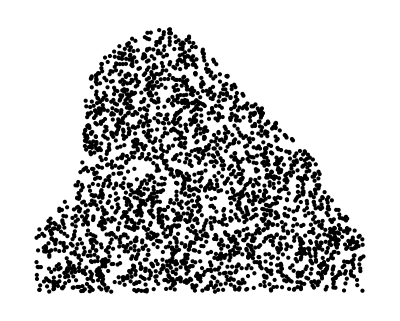

```mathematica
h=0.2;
θ=ArcSin[(0.5-h)/0.5];
min=If[h<0.5,0.5*Cos[-π-θ],-0.5];
max=If[h<0.5,0.5*Cos[θ],0.5];
{salt}=Last@
Reap@
Scan[
If[
(*#[[1]]^2+#[[2]]^3<2∧#[[1]]+#[[2]]<1,*)
Sow[#,"Salt"]
]&,RandomReal[{-2,2},{5000,2}]
];
Graphics[{Black,Point[salt]}]
```

```mathematica
h=0.2;
θ=ArcSin[(0.5-h)/0.5];
min=If[h<0.5,0.5*Cos[-π-θ],-0.5];
max=If[h<0.5,0.5*Cos[θ],0.5];
```